```mathematica
Needs["MFGraphs`"]
```

```mathematica
Get["/Users/ribeirrd/Dropbox/My Mac (kl-14835.kaust.edu.sa)/Documents/workspace/MFGraphs/MFGraphs/MFGraphs.m"](*Ricardo, use this when not running from eclipse.*)
```

```mathematica
FixedSolverStepX2[MFGEquations][{}]
```

```mathematica
MFGEquations["reduced system"]//Reduce//FullSimplify//BooleanConvert
```

```mathematica
Names["MFGraphs`*"]
```

{A,alpha,AtHead,AtTail,A$,beta,DataG,DataToEquations,EqEliminatorX,F,FixedPointSolverStepX,FixedSolverStepX2,g,g$2873,H,I1,I2,IncomingEdges,IncomingEdges$,Intg,m,m$,n,OtherWay,OutgoingEdges,OutgoingEdges$,p,Parameters,p$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,StartSolverX,Test,TransitionsAt,triple2path,U1,U2,V,V$2873,W,W$2873,x,x$}

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[25];
MFGEquations=DataToEquations[Data];
```

more stuff

#### This is the reduction of the system (in place of Reduce)

```mathematica
MFGEquations["Nrhs"]
```

{j248-j253+Intg[j248-j253],j250-j255+Intg[j250-j255]}

```mathematica
MFGEquations["reducing rules"]
```

{j248→0,j249→jt264,j250→2-jt264,j251→2-jt264,j252→2,j253→jt264,j254→0,j255→0,j256→0,j257→0,jt258→jt264,jt259→0,jt260→0,jt261→0,jt262→0,jt263→0,jt265→2-jt264,jt266→2-jt264,jt267→0,u269→1,u271→5,u274→1,u276→5,u277→u272}

```mathematica
reduced = FixedPoint[EqEliminatorX,{MFGEquations["EqAllAll"],{}},10]
```

{NonNegative[j220]&&NonNegative[2-j220]&&NonNegative[2-j220]&&NonNegative[j220]&&NonNegative[j220]&&NonNegative[j220]&&NonNegative[2-j220]&&NonNegative[2-j220]&&u235≤1&&u237≤u240&&u239≤u240&&u240≤u237&&u239≤u237&&u240≤∞&&u237≤∞&&u242≤5&&(j220==0||-1+u235==0)&&(j220==0||u239-u240==0)&&(2-j220==0||-u237+u239==0)&&(2-j220==0||-5+u242==0),{j215→0,j216→j220,j217→2-j220,j218→2-j220,j219→2,j221→0,j222→0,j223→0,j224→0,jt225→j220,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt231→j220,jt232→2-j220,jt233→2-j220,jt234→0,u236→1,u238→5,u241→1,u243→5,u244→u239}}

#### The critical congestion case (general numeric solver)

```mathematica
startrulesX=StartSolverX[MFGEquations]
AssociateTo[MFGEquations,"CriticalCongestionSolution"->First[startrulesX]];
```

{{j215→0,j216→2,j217→0,j218→0,j219→2,j220→2,j221→0,j222→0,j223→0,j224→0,jt225→2,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt231→2,jt232→0,jt233→0,jt234→0,u235→1,u236→1,u237→3,u238→5,u239→3,u240→3,u241→1,u242→3,u243→5,u244→3}}

#### Non-linear case

```mathematica
FixedSolverStepX2[MFGEquations][{}]
```

nonlinear: -jt231-u235+u240==-jt231+Intg[-jt231]&&2-jt231-u237+u242==2-jt231+Intg[2-jt231]

SYSTEM: -jt231-u235+u240==-jt231+Intg[-jt231]&&2-jt231-u237+u242==2-jt231+Intg[2-jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤u240&&u239≤u240&&u240≤u237&&u239≤u237&&u240≤∞&&u237≤∞&&u242≤5&&(jt231==0||-1+u235==0)&&(jt231==0||u239-u240==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-5+u242==0)

newsolve 2: {NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤u235+Intg[-jt231]&&u239≤u235+Intg[-jt231]&&u235+Intg[-jt231]≤u237&&u239≤u237&&u235+Intg[-jt231]≤∞&&u237≤∞&&u237+Intg[2-jt231]≤5&&(jt231==0||-1+u235==0)&&(jt231==0||-u235+u239-Intg[-jt231]==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-5+u237+Intg[2-jt231]==0),{j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u240→u235+Intg[-jt231],u241→1,u242→u237+Intg[2-jt231],u243→5,u244→u239}}

<|j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u240→u235+Intg[-jt231],u241→1,u242→u237+Intg[2-jt231],u243→5,u244→u239|>

```mathematica
Keys@MFGEquations
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,CurrentCompCon,EqCurrentCompCon,TransitionCompCon,EqTransitionCompCon,Compu,EqCompCon,EqAllComp,EqPosCon,CurrentSplitting,CurrentGathering,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EntryArgs,EntryDataAssociation,EqEntryIn,NonZeroEntryCurrents,ExitCosts,ExitValues,EqExitValues,SwitchingCosts,OutRules,InRules,Transu,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,jays,Nrhs,Nlhs,EqAllCompRules,EqAllRules,EqAllAll,EqAllAllSimple,RulesEntryIn,RulesExitValues,EqAllAllRules,reduced system,reducing rules,EqCriticalCaseRules,EqCriticalCase,CriticalCongestionSolution}

```mathematica
FixedSolverStepX2[MFGEquations][MFGEquations["CriticalCongestionSolution"]
]
```

ReplaceAll::reps: {Missing[KeyAbsent,CriticalCongestionSolution]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object {j248-j253+Intg[j248-j253],j250-j255+Intg[j250-j255]}/.Missing[KeyAbsent,CriticalCongestionSolution] at position {2, 2} in MapThread[#1==#2&,{{j248-j253-u268+u273,j250-j255-u270+u275},«1»/.Missing[KeyAbsent,CriticalCongestionSolution]}] has only 0 of required 1 dimensions.

nonlinear: #1==#2&&&{{j248-j253-u268+u273,j250-j255-u270+u275},{j248-j253+Intg[j248-j253],j250-j255+Intg[j250-j255]}/.Missing[KeyAbsent,CriticalCongestionSolution]}

SYSTEM: #1==#2&&&{{j248-j253-u268+u273,j250-j255-u270+u275},{j248-j253+Intg[j248-j253],j250-j255+Intg[j250-j255]}/.Missing[KeyAbsent,CriticalCongestionSolution]}&&NonNegative[jt264]&&NonNegative[2-jt264]&&NonNegative[2-jt264]&&NonNegative[jt264]&&NonNegative[jt264]&&NonNegative[jt264]&&NonNegative[2-jt264]&&NonNegative[2-jt264]&&u268≤1&&u270≤u273&&u272≤u273&&u273≤u270&&u272≤u270&&u273≤∞&&u270≤∞&&u275≤5&&(jt264==0||-1+u268==0)&&(jt264==0||u272-u273==0)&&(2-jt264==0||-u270+u272==0)&&(2-jt264==0||-5+u275==0)

ReplaceAll::reps: {Missing[KeyAbsent,CriticalCongestionSolution]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

newsolve 2: {#1==#2&&&{{-jt264-u268+u273,2-jt264-u270+u275},{-jt264+Intg[-jt264],2-jt264+Intg[2-jt264]}/.Missing[KeyAbsent,CriticalCongestionSolution]}&&NonNegative[jt264]&&NonNegative[2-jt264]&&NonNegative[2-jt264]&&NonNegative[jt264]&&NonNegative[jt264]&&NonNegative[jt264]&&NonNegative[2-jt264]&&NonNegative[2-jt264]&&u268≤1&&u270≤u273&&u272≤u273&&u273≤u270&&u272≤u270&&u273≤∞&&u270≤∞&&u275≤5&&(jt264==0||-1+u268==0)&&(jt264==0||u272-u273==0)&&(2-jt264==0||-u270+u272==0)&&(2-jt264==0||-5+u275==0),{j248→0,j249→jt264,j250→2-jt264,j251→2-jt264,j252→2,j253→jt264,j254→0,j255→0,j256→0,j257→0,jt258→jt264,jt259→0,jt260→0,jt261→0,jt262→0,jt263→0,jt265→2-jt264,jt266→2-jt264,jt267→0,u269→1,u271→5,u274→1,u276→5,u277→u272}}

<|j248→0,j249→jt264,j250→2-jt264,j251→2-jt264,j252→2,j253→jt264,j254→0,j255→0,j256→0,j257→0,jt258→jt264,jt259→0,jt260→0,jt261→0,jt262→0,jt263→0,jt265→2-jt264,jt266→2-jt264,jt267→0,u269→1,u271→5,u274→1,u276→5,u277→u272|>

```mathematica
MFGEquations["reducing rules"]
```

{j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u241→1,u243→5,u244→u239}

```mathematica
MFGEquations["reducing rules"]
```

{j116→0,j117→jt132,j118→2-jt132,j119→2-jt132,j120→2,j121→jt132,j122→0,j123→0,j124→0,j125→0,jt126→jt132,jt127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt133→2-jt132,jt134→2-jt132,jt135→0,u137→1,u139→5,u142→1,u144→5,u145→u140}

```mathematica
FixedPoint[FixedSolverStepX2[MFGEquations],MFGEquations["reducing rules"],10]
```

nonlinear: -jt231-u235+u240==-jt231+Intg[-jt231]&&2-jt231-u237+u242==2-jt231+Intg[2-jt231]

SYSTEM: -jt231-u235+u240==-jt231+Intg[-jt231]&&2-jt231-u237+u242==2-jt231+Intg[2-jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤u240&&u239≤u240&&u240≤u237&&u239≤u237&&u240≤∞&&u237≤∞&&u242≤5&&(jt231==0||-1+u235==0)&&(jt231==0||u239-u240==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-5+u242==0)

newsolve 2: {NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤u235+Intg[-jt231]&&u239≤u235+Intg[-jt231]&&u235+Intg[-jt231]≤u237&&u239≤u237&&u235+Intg[-jt231]≤∞&&u237≤∞&&u237+Intg[2-jt231]≤5&&(jt231==0||-1+u235==0)&&(jt231==0||-u235+u239-Intg[-jt231]==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-5+u237+Intg[2-jt231]==0),{j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u240→u235+Intg[-jt231],u241→1,u242→u237+Intg[2-jt231],u243→5,u244→u239}}

nonlinear: -jt231-u235+u240==-jt231+Intg[-jt231]&&2-jt231-u237+u242==2-jt231+Intg[2-jt231]

SYSTEM: -jt231-u235+u240==-jt231+Intg[-jt231]&&2-jt231-u237+u242==2-jt231+Intg[2-jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤u240&&u239≤u240&&u240≤u237&&u239≤u237&&u240≤∞&&u237≤∞&&u242≤5&&(jt231==0||-1+u235==0)&&(jt231==0||u239-u240==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-5+u242==0)

newsolve 2: {NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤u235+Intg[-jt231]&&u239≤u235+Intg[-jt231]&&u235+Intg[-jt231]≤u237&&u239≤u237&&u235+Intg[-jt231]≤∞&&u237≤∞&&u237+Intg[2-jt231]≤5&&(jt231==0||-1+u235==0)&&(jt231==0||-u235+u239-Intg[-jt231]==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-5+u237+Intg[2-jt231]==0),{j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u240→u235+Intg[-jt231],u241→1,u242→u237+Intg[2-jt231],u243→5,u244→u239}}

<|j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u240→u235+Intg[-jt231],u241→1,u242→u237+Intg[2-jt231],u243→5,u244→u239|>

```mathematica
MFGEquations["Nrhs"]
```

{-jt231+Intg[-jt231],2-jt231+Intg[2-jt231]}

```mathematica
Eqs=MFGEquations;
```

```mathematica
And @@MapThread[(Equal[#1,#2])&,{Eqs["Nlhs"],(Eqs["Nrhs"]/.Eqs)}]
```

j39-j42-u49+u52==j39-j42+Intg[j39-j42]

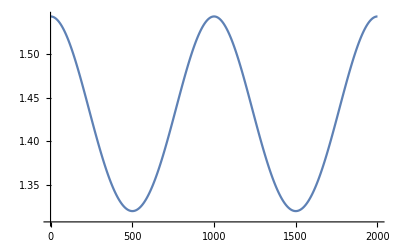

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

```mathematica
MFGEquations["Nlhs"]
```

{-jt198-u202+u207,2-jt198-u204+u209}

```mathematica
MFGEquations["EqCriticalCase"]
```

-jt198-u202+u207==0&&2-jt198-u204+u209==0

```mathematica
MFGEquations["criticalreduced"]
```

{NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[jt231]&&NonNegative[2-jt231]&&NonNegative[2-jt231]&&u235≤1&&u237≤jt231+u235&&u239≤jt231+u235&&jt231+u235≤u237&&u239≤u237&&jt231+u235≤∞&&u237≤∞&&-2+jt231+u237≤5&&(jt231==0||-1+u235==0)&&(jt231==0||-jt231-u235+u239==0)&&(2-jt231==0||-u237+u239==0)&&(2-jt231==0||-7+jt231+u237==0),{j215→0,j216→jt231,j217→2-jt231,j218→2-jt231,j219→2,j220→jt231,j221→0,j222→0,j223→0,j224→0,jt225→jt231,jt226→0,jt227→0,jt228→0,jt229→0,jt230→0,jt232→2-jt231,jt233→2-jt231,jt234→0,u236→1,u238→5,u240→jt231+u235,u241→1,u242→-2+jt231+u237,u243→5,u244→u239}}

```mathematica
reduced[[2]]
```

{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}

```mathematica
FixedPointSolverStepX[MFGEquations][{reduced[[2]]}]
```

95-u61==64.1073

95-u61==64.1073&&u61≤u61&&u61≤∞

ReplaceAll::reps: {95-u61==64.1073&&{j49==80,j50==80,j51==80,j52==0,j53==0,j54==0,«3»,jt58==0,u59==u61,u60==15,u62==15,u63==15,u64==u61}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{95-u61==64.1073&&u61≤u61&&u61≤∞/.95-u61==64.1073&&{j49==80,j50==80,j51==80,j52==0,j53==0,j54==0,jt55==0,jt56==80,jt57==80,jt58==0,u59==u61,u60==15,u62==15,u63==15,u64==u61},95-u61==64.1073&&{j49==80,j50==80,j51==80,j52==0,j53==0,j54==0,jt55==0,jt56==80,jt57==80,jt58==0,u59==u61,u60==15,u62==15,u63==15,u64==u61}}

{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}

```mathematica
x/.{x->2, x->3}
```

2

```mathematica
As=<|x->2,x->3|>;
As[x]
```

```mathematica
x/.As
```

3

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.

```mathematica
Association@{x->3, x->4}
```

<|x→4|>

```mathematica
Association@As
```

<|x→3|>